```mathematica
stillLifeCondition[i_,j_]:=(b[i,j]&&NeighborCount[{2,3},{i,j}])||(!b[i,j]&&!NeighborCount[{3},{i,j}]);
```

(b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&b[1+i,1+j])

```mathematica
life44
```

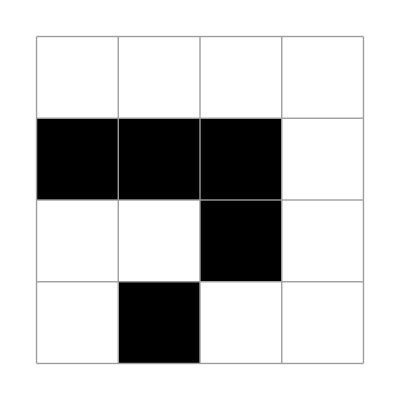
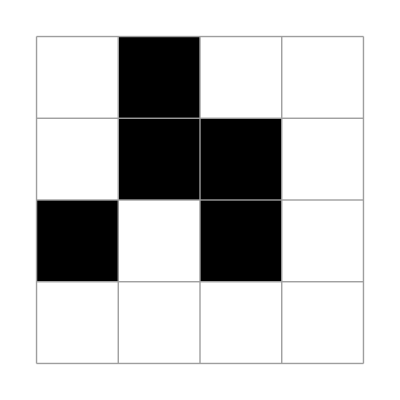
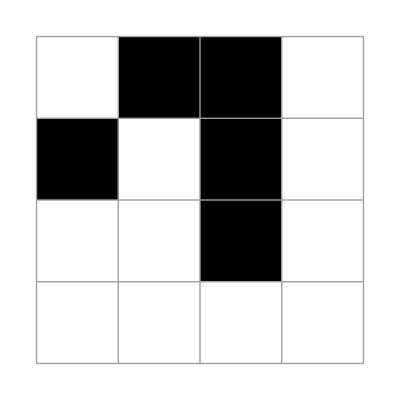
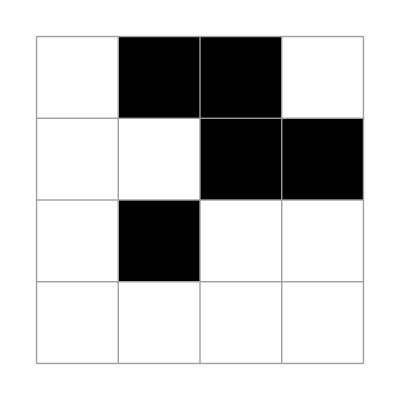

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```